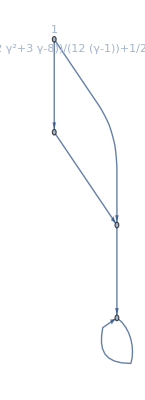

1/2+(γ (-8+3 γ-2 γ^2+γ^3))/(12 (-1+γ))

```mathematica
(*Be sure to run "runThisFileFirst.nb"*)
(*To Run, press Shift+Enter. Or, at top, Evaluation -> Evaluate Cells*)
(*Note: If running forever,(usually #states > 7), then Evaluation -> Quit Kernal -> local*)
vertexAndNodes = {1->2,1->3, 2->3, 3->4, 4->4};

(*            graph    , First/All, None/Basic*)
powerOfGraph[vertexAndNodes, "First", "None"]
(*
First - calculate Power for first state only;
All - Calcuate Power for all states;
None - Display only final power graph;
Basic - Display basic info such as frequency vector, inequalities, and integrations.
*)

(*If you'd like to compare a handwritten equation with the calculated power:*)
eq = 2/3*γ + 5/12*γ^2 + 7/12*γ^3 + 1/2 *γ^4/(1-γ);
powerCheck[eq]
(*Note: use the ";" at the end to suppress output*)
```